```mathematica
SetDirectory[NotebookDirectory[]]
Needs["HierarchicalClustering`"]
```

/Users/hayssam/Documents/ISOP_0.2/tests

```mathematica
pwCoords=Import["coordinates.tsv"];
```

```mathematica
Dimensions[pwCoords]
```

{232,501}

```mathematica
clusterables=(#[[2;;]]-> #[[1]])&/@ pwCoords;
```

```mathematica
labels=pwCoords[[All,1]]
```

```mathematica
clusterables[[1]]
```

```mathematica
FindClusters[clusterables]
```

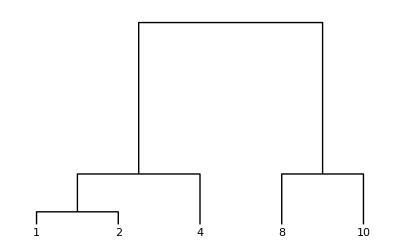

```mathematica
DendrogramPlot[{1,2,10,4,8},LeafLabels->{1,2,10,4,8}]
```

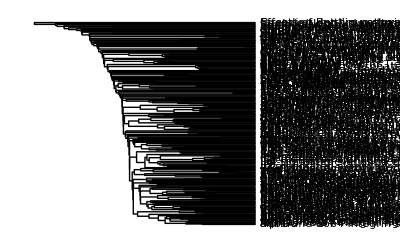

```mathematica
DendrogramPlot[pwCoords[[All,2;;]],LeafLabels->pwCoords[[All,1]],Orientation->Left,DistanceFunction->CosineDistance]
```

```mathematica
clusterables[[1]]
```

```mathematica
clusters=FindClusters[clusterables,DistanceFunction->CosineDistance]
```

{{alpha6,Plasma membrane estrogen receptor signaling,Alpha6 beta4 integrin-ligand interactions,Signaling events mediated by VEGFR1 and VEGFR2,a6b1 and a6b4 Integrin signaling,E-cadherin signaling in the nascent adherens junction,Syndecan-2-mediated signaling events,EPHA2 forward signaling,VEGFR3 signaling in lymphatic endothelium,Alpha4 beta1 integrin signaling events,RAC1 signaling pathway,Endothelins,Signaling events mediated by PRL,RhoA signaling pathway,Thromboxane A2 receptor signaling,Beta2 integrin cell surface interactions,Urokinase-type plasminogen activator (uPA) and uPAR-mediated signaling,Lissencephaly gene (LIS1) in neuronal migration and development,Syndecan-4-mediated signaling events,Syndecan-1-mediated signaling events,Beta1 integrin cell surface interactions,LPA receptor mediated events,CDC42 signaling events,Integrins in angiogenesis,amb2 Integrin signaling,Glypican 2 network,Netrin-mediated signaling events,E-cadherin signaling in keratinocytes,EPHA forward signaling,Reelin signaling pathway,Regulation of RhoA activity,Integrin-linked kinase signaling,Nectin adhesion pathway,Class IB PI3K non-lipid kinase events,Arf6 downstream pathway,Alpha9 beta1 integrin signaling events,Visual signal transduction: Cones,Signaling events mediated by focal adhesion kinase,PAR1-mediated thrombin signaling events,IGF1 pathway,Angiopoietin receptor Tie2-mediated signaling,VEGFR1 specific signals,Stabilization and expansion of the E-cadherin adherens junction,Arf6 signaling events,Nephrin/Neph1 signaling in the kidney podocyte,Nongenotropic Androgen signaling,Beta5 beta6 beta7 and beta8 integrin cell surface interactions,a4b7 Integrin signaling,Class I PI3K signaling events mediated by Akt,Regulation of CDC42 activity,EPHB forward signaling,Signaling events regulated by Ret tyrosine kinase,Beta3 integrin cell surface interactions,N-cadherin signaling events,Glypican 1 network,Noncanonical Wnt signaling pathway,VEGF and VEGFR signaling network,Regulation of RAC1 activity,Osteopontin-mediated events,PAR4-mediated thrombin signaling events,Ephrin B reverse signaling,Ephrin A  reverse signaling},{ar,notch,id,tgfb,wnt,hedgehog,unknown,DNA-PK pathway in nonhomologous end joining,HIF-2-alpha transcription factor network,E2F transcription factor network,ATR signaling pathway,Validated transcriptional targets of deltaNp63 isoforms,Effects of Botulinum toxin,PLK3 signaling events,Regulation of retinoblastoma protein,Fanconi anemia pathway,Regulation of nuclear SMAD2/3 signaling,AP-1 transcription factor network,ATF-2 transcription factor network,Notch-mediated HES/HEY network,FOXM1 transcription factor network,FOXA1 transcription factor network,ALK2 signaling events,HIV-1 Nef: Negative effector of Fas and TNF-alpha,C-MYB transcription factor network,p73 transcription factor network,Notch signaling pathway,Aurora B signaling,PLK1 signaling events,Signaling events mediated by HDAC Class II,p75(NTR)-mediated signaling,FAS (CD95) signaling pathway,Circadian rhythm pathway,RXR and RAR heterodimerization with other nuclear receptor,Signaling events mediated by HDAC Class I,Regulation of Telomerase,FOXA2 and FOXA3 transcription factor networks,TRAIL signaling pathway,ALK1 signaling events,Hypoxic and oxygen homeostasis regulation of HIF-1-alpha,BMP receptor signaling,Presenilin action in Notch and Wnt signaling,Aurora C signaling,Wnt signaling network,mTOR signaling pathway,Glucocorticoid receptor regulatory network,Regulation of nuclear beta catenin signaling and target gene transcription,Regulation of cytoplasmic and nuclear SMAD2/3 signaling,PLK2 and PLK4 events,ATM pathway,LKB1 signaling events,Canonical Wnt signaling pathway,Caspase cascade in apoptosis,Hedgehog signaling events mediated by Gli proteins,Signaling events mediated by the Hedgehog family,Retinoic acid receptors-mediated signaling,Direct p53 effectors,Regulation of Androgen receptor activity,Sumoylation by RanBP2 regulates transcriptional repression,Glypican 3 network,BARD1 signaling events,Validated transcriptional targets of TAp63 isoforms,Coregulation of Androgen receptor activity,Validated targets of C-MYC transcriptional activation,Degradation of beta catenin,Signaling events mediated by HDAC Class III,FoxO family signaling,C-MYC pathway,Aurora A signaling,Validated targets of C-MYC transcriptional repression,HIF-1-alpha transcription factor network,p53 pathway,Cellular roles of Anthrax toxin,Validated transcriptional targets of AP1 family members Fra1 and Fra2,Endogenous TLR signaling},{egfr,kit,tnf,il6,leptin,tsh,fsh,Trk receptor signaling mediated by PI3K and PLC-gamma,Alpha-synuclein signaling,FGF signaling pathway,ErbB1 downstream signaling,ErbB2/ErbB3 signaling events,TGF-beta receptor signaling,ErbB receptor signaling network,p38 signaling mediated by MAPKAP kinases,Insulin Pathway,Visual signal transduction: Rods,PDGFR-alpha signaling pathway,Regulation of p38-alpha and p38-beta,EGF receptor (ErbB1) signaling pathway,Signaling events mediated by TCPTP,Signaling mediated by p38-alpha and p38-beta,Signaling events mediated by Stem cell factor receptor (c-Kit),Neurotrophic factor-mediated Trk receptor signaling,p38 MAPK signaling pathway,Internalization of ErbB1,IL8- and CXCR2-mediated signaling events,Signaling mediated by p38-gamma and p38-delta,ErbB4 signaling events,EGFR-dependent Endothelin signaling events,Ceramide signaling pathway,Posttranslational regulation of adherens junction stability and dissassembly,Signaling events mediated by Hepatocyte Growth Factor Receptor (c-Met),Signaling events mediated by PTP1B,PDGFR-beta signaling pathway,TNF receptor signaling pathway,Ras signaling in the CD4+ TCR pathway,Rapid glucocorticoid signaling,Arf1 pathway,Insulin-mediated glucose transport,IL8- and CXCR1-mediated signaling events,Syndecan-3-mediated signaling events,PDGF receptor signaling network,Arf6 trafficking events,Trk receptor signaling mediated by the MAPK pathway},{tcell,bcell,il1,rankl,CD40/CD40L signaling,Canonical NF-kappaB pathway,Calcium signaling in the CD4+ TCR pathway,Fc-epsilon receptor I signaling in mast cells,BCR signaling pathway,IL1-mediated signaling events,Role of Calcineurin-dependent NFAT signaling in lymphocytes,CXCR4-mediated signaling events,JNK signaling in the CD4+ TCR pathway,TCR signaling in na&#xef;ve CD8+ T cells,Calcineurin-regulated NFAT-dependent transcription in lymphocytes,AlphaE beta7 integrin cell surface interactions,Alternative NF-kappaB pathway,TCR signaling in na&#xef;ve CD4+ T cells,Atypical NF-kappaB pathway,Class I PI3K signaling events},{il2,il3,il4,il5,il7,il9,tslp,IL2 signaling events mediated by STAT5,Downstream signaling in na&#xef;ve CD8+ T cells,IL12 signaling mediated by STAT4,IL23-mediated signaling events,GMCSF-mediated signaling events,IFN-gamma pathway,IL6-mediated signaling events,IL3-mediated signaling events,IL27-mediated signaling events,IL2-mediated signaling events,IL2 signaling events mediated by PI3K,IL12-mediated signaling events,IL4-mediated signaling events,EPO signaling pathway,IL5-mediated signaling events},{Sphingosine 1-phosphate (S1P) pathway,S1P1 pathway,CXCR3-mediated signaling events,S1P5 pathway,S1P4 pathway,S1P3 pathway,LPA4-mediated signaling events,S1P2 pathway}}

```mathematica
Length /@ clusters
```

{62,75,45,20,22,8}

```mathematica
clusters[[1]]//MatrixForm
clusters[[2]]//MatrixForm
clusters[[3]]//MatrixForm
clusters[[4]]//MatrixForm
```

(alpha6
Plasma membrane estrogen receptor signaling
Alpha6 beta4 integrin-ligand interactions
Signaling events mediated by VEGFR1 and VEGFR2
a6b1 and a6b4 Integrin signaling
E-cadherin signaling in the nascent adherens junction
Syndecan-2-mediated signaling events
EPHA2 forward signaling
VEGFR3 signaling in lymphatic endothelium
Alpha4 beta1 integrin signaling events
RAC1 signaling pathway
Endothelins
Signaling events mediated by PRL
RhoA signaling pathway
Thromboxane A2 receptor signaling
Beta2 integrin cell surface interactions
Urokinase-type plasminogen activator (uPA) and uPAR-mediated signaling
Lissencephaly gene (LIS1) in neuronal migration and development
Syndecan-4-mediated signaling events
Syndecan-1-mediated signaling events
Beta1 integrin cell surface interactions
LPA receptor mediated events
CDC42 signaling events
Integrins in angiogenesis
amb2 Integrin signaling
Glypican 2 network
Netrin-mediated signaling events
E-cadherin signaling in keratinocytes
EPHA forward signaling
Reelin signaling pathway
Regulation of RhoA activity
Integrin-linked kinase signaling
Nectin adhesion pathway
Class IB PI3K non-lipid kinase events
Arf6 downstream pathway
Alpha9 beta1 integrin signaling events
Visual signal transduction: Cones
Signaling events mediated by focal adhesion kinase
PAR1-mediated thrombin signaling events
IGF1 pathway
Angiopoietin receptor Tie2-mediated signaling
VEGFR1 specific signals
Stabilization and expansion of the E-cadherin adherens junction
Arf6 signaling events
Nephrin/Neph1 signaling in the kidney podocyte
Nongenotropic Androgen signaling
Beta5 beta6 beta7 and beta8 integrin cell surface interactions
a4b7 Integrin signaling
Class I PI3K signaling events mediated by Akt
Regulation of CDC42 activity
EPHB forward signaling
Signaling events regulated by Ret tyrosine kinase
Beta3 integrin cell surface interactions
N-cadherin signaling events
Glypican 1 network
Noncanonical Wnt signaling pathway
VEGF and VEGFR signaling network
Regulation of RAC1 activity
Osteopontin-mediated events
PAR4-mediated thrombin signaling events
Ephrin B reverse signaling
Ephrin A  reverse signaling)

(ar
notch
id
tgfb
wnt
hedgehog
unknown
DNA-PK pathway in nonhomologous end joining
HIF-2-alpha transcription factor network
E2F transcription factor network
ATR signaling pathway
Validated transcriptional targets of deltaNp63 isoforms
Effects of Botulinum toxin
PLK3 signaling events
Regulation of retinoblastoma protein
Fanconi anemia pathway
Regulation of nuclear SMAD2/3 signaling
AP-1 transcription factor network
ATF-2 transcription factor network
Notch-mediated HES/HEY network
FOXM1 transcription factor network
FOXA1 transcription factor network
ALK2 signaling events
HIV-1 Nef: Negative effector of Fas and TNF-alpha
C-MYB transcription factor network
p73 transcription factor network
Notch signaling pathway
Aurora B signaling
PLK1 signaling events
Signaling events mediated by HDAC Class II
p75(NTR)-mediated signaling
FAS (CD95) signaling pathway
Circadian rhythm pathway
RXR and RAR heterodimerization with other nuclear receptor
Signaling events mediated by HDAC Class I
Regulation of Telomerase
FOXA2 and FOXA3 transcription factor networks
TRAIL signaling pathway
ALK1 signaling events
Hypoxic and oxygen homeostasis regulation of HIF-1-alpha
BMP receptor signaling
Presenilin action in Notch and Wnt signaling
Aurora C signaling
Wnt signaling network
mTOR signaling pathway
Glucocorticoid receptor regulatory network
Regulation of nuclear beta catenin signaling and target gene transcription
Regulation of cytoplasmic and nuclear SMAD2/3 signaling
PLK2 and PLK4 events
ATM pathway
LKB1 signaling events
Canonical Wnt signaling pathway
Caspase cascade in apoptosis
Hedgehog signaling events mediated by Gli proteins
Signaling events mediated by the Hedgehog family
Retinoic acid receptors-mediated signaling
Direct p53 effectors
Regulation of Androgen receptor activity
Sumoylation by RanBP2 regulates transcriptional repression
Glypican 3 network
BARD1 signaling events
Validated transcriptional targets of TAp63 isoforms
Coregulation of Androgen receptor activity
Validated targets of C-MYC transcriptional activation
Degradation of beta catenin
Signaling events mediated by HDAC Class III
FoxO family signaling
C-MYC pathway
Aurora A signaling
Validated targets of C-MYC transcriptional repression
HIF-1-alpha transcription factor network
p53 pathway
Cellular roles of Anthrax toxin
Validated transcriptional targets of AP1 family members Fra1 and Fra2
Endogenous TLR signaling)

(egfr
kit
tnf
il6
leptin
tsh
fsh
Trk receptor signaling mediated by PI3K and PLC-gamma
Alpha-synuclein signaling
FGF signaling pathway
ErbB1 downstream signaling
ErbB2/ErbB3 signaling events
TGF-beta receptor signaling
ErbB receptor signaling network
p38 signaling mediated by MAPKAP kinases
Insulin Pathway
Visual signal transduction: Rods
PDGFR-alpha signaling pathway
Regulation of p38-alpha and p38-beta
EGF receptor (ErbB1) signaling pathway
Signaling events mediated by TCPTP
Signaling mediated by p38-alpha and p38-beta
Signaling events mediated by Stem cell factor receptor (c-Kit)
Neurotrophic factor-mediated Trk receptor signaling
p38 MAPK signaling pathway
Internalization of ErbB1
IL8- and CXCR2-mediated signaling events
Signaling mediated by p38-gamma and p38-delta
ErbB4 signaling events
EGFR-dependent Endothelin signaling events
Ceramide signaling pathway
Posttranslational regulation of adherens junction stability and dissassembly
Signaling events mediated by Hepatocyte Growth Factor Receptor (c-Met)
Signaling events mediated by PTP1B
PDGFR-beta signaling pathway
TNF receptor signaling pathway
Ras signaling in the CD4+ TCR pathway
Rapid glucocorticoid signaling
Arf1 pathway
Insulin-mediated glucose transport
IL8- and CXCR1-mediated signaling events
Syndecan-3-mediated signaling events
PDGF receptor signaling network
Arf6 trafficking events
Trk receptor signaling mediated by the MAPK pathway)

(tcell
bcell
il1
rankl
CD40/CD40L signaling
Canonical NF-kappaB pathway
Calcium signaling in the CD4+ TCR pathway
Fc-epsilon receptor I signaling in mast cells
BCR signaling pathway
IL1-mediated signaling events
Role of Calcineurin-dependent NFAT signaling in lymphocytes
CXCR4-mediated signaling events
JNK signaling in the CD4+ TCR pathway
TCR signaling in na&#xef;ve CD8+ T cells
Calcineurin-regulated NFAT-dependent transcription in lymphocytes
AlphaE beta7 integrin cell surface interactions
Alternative NF-kappaB pathway
TCR signaling in na&#xef;ve CD4+ T cells
Atypical NF-kappaB pathway
Class I PI3K signaling events)

```mathematica
clusters[[5]]//MatrixForm
clusters[[6]]//MatrixForm
```

(il2
il3
il4
il5
il7
il9
tslp
IL2 signaling events mediated by STAT5
Downstream signaling in na&#xef;ve CD8+ T cells
IL12 signaling mediated by STAT4
IL23-mediated signaling events
GMCSF-mediated signaling events
IFN-gamma pathway
IL6-mediated signaling events
IL3-mediated signaling events
IL27-mediated signaling events
IL2-mediated signaling events
IL2 signaling events mediated by PI3K
IL12-mediated signaling events
IL4-mediated signaling events
EPO signaling pathway
IL5-mediated signaling events)

(Sphingosine 1-phosphate (S1P) pathway
S1P1 pathway
CXCR3-mediated signaling events
S1P5 pathway
S1P4 pathway
S1P3 pathway
LPA4-mediated signaling events
S1P2 pathway)